```mathematica
m =1;
MOI = 1;
d = 1;
g=9.81;
vec[p_,th_]:={-m g d Sin[th],p/MOI}
```

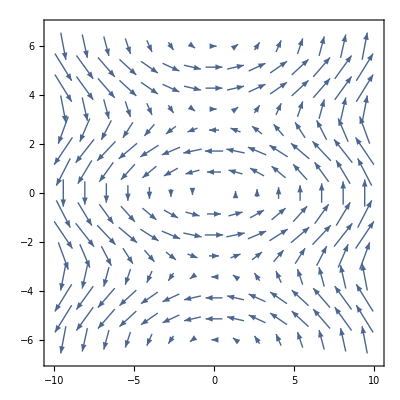

```mathematica
VectorPlot[vec[p,th],{p,-3Pi,3Pi},{th,-6,6}]
```

```mathematica
vec[p,th]
```

{-9.81 Sin[th],p}